IdentityElement[group_]:=Module[{elems,n},Which[(*Groupes finis standard*)Head[group]===CyclicGroup,0,Head[group]===DihedralGroup,Cycles[{}],Head[group]===SymmetricGroup||Head[group]===AlternatingGroup,Cycles[{}],(*PermutationGroup*)Head[group]===PermutationGroup,Cycles[{}],(*AbelianGroup*)Head[group]===AbelianGroup||(ValueQ[AbelianGroupQ[_]]&&TrueQ[AbelianGroupQ[group]]),Table[0,{i,Length[group[[1]]]}],(*(Zn,+):groupe additif modulo n*)MatchQ[group,{"AddMod",n_}],0,(*(Zn,×) monoïde ou groupe multiplicatif*)MatchQ[group,{"MultMod",n_}],1,(*Cas général:prendre le premier élément de GroupElements*)True,First[GroupElements[group]]]]

IsIdentityByGroup[group_,elem_]:=(elem===IdentityElement[group])

IsIdentity[list_List,elem_,operation_:Plus]/;MemberQ[list,elem]:=AllTrue[list,((operation[elem,#])==#&)]

IsCenter[group_,elem_]/;GroupElementQ[group,elem]:=AllTrue[GroupElements[group],((PermutationProduct[elem,#])==PermutationProduct[#,elem]&)]

GroupCenter[group_]:=Select[GroupElements[group],IsCenter[group,#]&]

AbelianGroupQ[group_]:=GroupElements[group]==GroupCenter[group]

CayleyMultiplicationTable[group_]:=Module[{elements,Operation,n,i,table,opSymbol},(*Détection du type de groupe et définition de l'opération*)Which[(*Groupe abélien*)Head[group]===AbelianGroup||(ValueQ[AbelianGroupQ[_]]&&TrueQ[AbelianGroupQ[group]]),n=group[[1]];
elements=Tuples[Table[Range[0,n[[i]]-1],{i,Length[n]}]];
Operation[x_,y_]:=Mod[x+y,n];
opSymbol="+ (mod "<>ToString[n]<>")",(*Groupe cyclique*)Head[group]===CyclicGroup,elements=Range[0,group[[1]]-1];
Operation[x_,y_]:=Mod[x+y,group[[1]]];
opSymbol="+ (mod "<>ToString[group[[1]]]<>")",(*Groupes modulaires personnalisés*)MatchQ[group,{_String,_Integer}],elements=Range[0,group[[2]]-1];
Operation[x_,y_]:=Which[group[[1]]=="AddMod",Mod[x+y,group[[2]]],group[[1]]=="MultMod",Mod[x*y,group[[2]]]];
opSymbol=Which[group[[1]]=="AddMod","+ (mod "<>ToString[group[[2]]]<>")",group[[1]]=="MultMod","× (mod "<>ToString[group[[2]]]<>")"],(*Domaine Booléen*)MatchQ[group,{_String,_String}],elements={True,False};
Operation[x_,y_]:=Which[group[[1]]=="And",And[x,y],group[[1]]=="Or",Or[x,y],group[[1]]=="Xor",Xor[x,y]];
opSymbol=group[[1]],(*Groupes de permutations*)MemberQ[{DihedralGroup,SymmetricGroup,AlternatingGroup,PermutationGroup},Head[group]],elements=GroupElements[group];
Operation[x_,y_]:=PermutationProduct[x,y];
opSymbol="∘"];
(*Construction de la table avec en-têtes*)table=Prepend[MapIndexed[Prepend[#,elements[[First[#2]]]]&,Table[Operation[elements[[i]],elements[[j]]],{i,Length[elements]},{j,Length[elements]}]],Prepend[elements,Style[opSymbol,Bold]]  (*Case supérieure gauche avec couleur*)];
Grid[table,Frame->All,Spacings->{2,2}]]

background[val_,listeCouleurs_]:=Framed[val,Background->listeCouleurs[[val+1]]]

ColoredCayleyTable[{_,n_Integer}]:=Module[{table,elements,couleurs},elements=Range[0,n-1];
couleurs=ColorData["AlpineColors"]/@Subdivide[0,1,n-1];
table=Prepend[MapIndexed[Prepend[#,elements[[First[#2]]]]&,Table[background[Mod[Times[i,j],n],couleurs],{i,0,n-1},{j,0,n-1}]],Prepend[elements,Style["Multiplication mod "<>ToString[n],Bold]]];
Grid[table,Frame->All,Spacings->{1,1}]]

# Group Theory Add-On for Mathematica - Applications Exploring Groups with Mathematica : from Music to Particles

## Jules Charlier, Rafael Salavarria Lorenzoni, Oscar Eatwell, Jawad Ben Brahim

## Group Theory : Basics

Théorie abstraite des maths apparue fin XVIIIè s, vu son essor au XXè s, nombreuses applications utiles dans domaines variés

1. Binary operation : 
2. Neutral element - Identity : 
3. Inverses :

```mathematica
ColoredCayleyTable[{"MultMod", 8}]
```

Multiplication mod 8 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7
2 | 0 | 2 | 4 | 6 | 0 | 2 | 4 | 6
3 | 0 | 3 | 6 | 1 | 4 | 7 | 2 | 5
4 | 0 | 4 | 0 | 4 | 0 | 4 | 0 | 4
5 | 0 | 5 | 2 | 7 | 4 | 1 | 6 | 3
6 | 0 | 6 | 4 | 2 | 0 | 6 | 4 | 2
7 | 0 | 7 | 6 | 5 | 4 | 3 | 2 | 1

## Generators

### Musical scales and intervals, and generators

Traditionnaly in music theory an octave is deivided into 12 named intervals. After which we loop back to C, which means it behaves similarly to ℤ/12ℤ

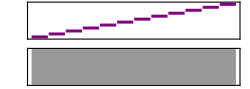

```mathematica
Sound[Table[SoundNote[n,0.5],{n,0,11}]]
```

If we consider the operation of stacking two intervals on top of each other as a group operation, then this scale is isomorphic to (ℤ/12ℤ,+)≅C_12, which we can represent in a Cailey table:

```mathematica
TableForm[GroupMultiplicationTable[CyclicGroup[12]] -1,TableHeadings->{Range[0,11],Range[0,11]}]
```

| 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11
0 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11
1 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 0
2 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 0 | 1
3 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 0 | 1 | 2
4 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 0 | 1 | 2 | 3
5 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 0 | 1 | 2 | 3 | 4
6 | 6 | 7 | 8 | 9 | 10 | 11 | 0 | 1 | 2 | 3 | 4 | 5
7 | 7 | 8 | 9 | 10 | 11 | 0 | 1 | 2 | 3 | 4 | 5 | 6
8 | 8 | 9 | 10 | 11 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7
9 | 9 | 10 | 11 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
10 | 10 | 11 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
11 | 11 | 0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10

Let’s try to stack the same interval on top of itself many times, and see the intervals we get by this process:

```mathematica
Manipulate[
Column[
{
Sound[
{Table[SoundNote[Mod[k n,12],1],{k,0,11}]}
],
UniqueElements[{Table[Mod[k n,12],{k,0,11}]}][[1]]
}
],
{n,0,11,1}
]
```

```mathematica
Manipulate[
Column[
{
StringJoin["PGCD(",ToString[n],",12) = ",ToString[GCD[12,n]]],
UniqueElements[{Table[Mod[k n,12],{k,12}]}][[1]]
}
],
{n,0,11,1}
]
```

```mathematica
Manipulate[
Column[
{
StringJoin["12 / PGCD(",ToString[n],",12) = ",ToString[12/GCD[12,n]]],
UniqueElements[{Table[Mod[k n,12],{k,12}]}][[1]]
}
],
{n,0,11,1}
]
```

```mathematica
(*Calculate b and c numerically*){b,c}=N@{E^((-Log[220]+Log[440])/12),(3 (-3 Log[220]-Log[440]))/(Log[220]-Log[440])};

(*Define frequency function*)
frequency[x_?NumericQ]:=b^(x+c)
Manipulate[
Module[
{tones},
tones=Table[
With[
{k=n},
Play[
Sin[2 Pi t*frequency[12.0*k/m]],
{t,0,0.5},
SampleRate->8000
]
],
{n,0,m-1}
];
Sound[tones]
(*a list of Sound objects plays in sequence*)
],
{{m,12},2,50,1}
]
```

## Symmetry Groups

Triangle équilatéral 
Rotations + Reflections -> animations 2D @Jawad triangle

## Our Add-On

Cayley Table

```mathematica
Quiet@CayleyMultiplicationTable[{"AddMod",7}]
Quiet@CayleyMultiplicationTable[DihedralGroup[3]]
```

## U(1) et SU(2) : when Physics meets Group Theory

- U(1) : phases on a circle

- SU(2) : spin rotations

## Games & Puzzles

15 puzzle “taquin” (sliding puzzle) --> permutations, Alternating Group

## Key features - Conclusion

Prise en compte d’un grand nombre de groupes dans nos fonctions, syntaxe claire, rendus esthétiques, pas d’erreurs